# Interacting Dark Energy with a Quadratic EoS with a Late-Time Cosmological Constant

## Manipulate Plots

#### Non-Compact x - z Phase Space

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,z→0},{x→(-1-wx)/ϵ,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ+3 ℛ ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-q (1+wx) ℛ-(9 ϵ)/q | -3
((-3+q ℛ) (q+q wx+3 ϵ))/q | 0) | ((-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)
(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)) | (-(q^2 ℛ+q^2 wx ℛ+9 ϵ+√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1
-(q^2 ℛ+q^2 wx ℛ+9 ϵ-√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1)
(ℛ
0) | (-3 (1+wx+ℛ ϵ) | -q ℛ
0 | -3+q ℛ) | (-3+q ℛ
-3 (1+wx+ℛ ϵ)) | (-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | 1
1 | 0)
((-1-wx)/ϵ
0) | (3 (1+wx+ℛ ϵ) | (q (1+wx))/ϵ
0 | -(q+q wx+3 ϵ)/ϵ) | ((-q-q wx-3 ϵ)/ϵ
3 (1+wx+ℛ ϵ)) | (-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | 1
1 | 0)

```mathematica
(*Find the condition for spiral fixed point to be complex*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{ϵ,q,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ϵ→1/9 (-6 q+q^2 ℛ-q^2 wx ℛ-2 √(-9 q^2 wx+6 q^3 wx ℛ-q^4 wx ℛ^2))},{ϵ→1/9 (-6 q+q^2 ℛ-q^2 wx ℛ+2 √(-9 q^2 wx+6 q^3 wx ℛ-q^4 wx ℛ^2))}}

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[wx_,q_,ϵ_,ℛ_]=dex;
DM[q_]=dez;
```

```mathematica
(*Plot the phase space for the dark energy and the dark matter*)
Manipulate[StreamPlot[{DE[wx,q,ϵ,ℛ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ},{x→3/q,y→-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ-3 ℛ ϵ) | -q x z-3 (x-ℛ) (1+wx+x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ) | (0 | -3 (x-ℛ) (1+wx+x ϵ)+q x (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | -1/6
0 | -((-3+q x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 0) | (0
-(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)
(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)) | (-1/(1+3 wx+6 x ϵ-3 ℛ ϵ) | 0 | 1
-(-3 x-3 wx x+q x^2+3 q wx x^2+3 ℛ+3 wx ℛ-3 q x ℛ-3 q wx x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | (√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1
-(-3 x-3 wx x+q x^2+3 q wx x^2+3 ℛ+3 wx ℛ-3 q x ℛ-3 q wx x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | -(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1)
(3/q
-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (((q^2 (1+wx) ℛ+9 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | (√3 √(q^2 (1+wx) ℛ-9 ϵ-3 q (wx-ℛ ϵ)))/q
1/6 (-1-3 wx-(18 ϵ)/q+3 ℛ ϵ) | (2 √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q | -1/6
-((-3+q ℛ) (q+q wx+3 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | 0) | ((2 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)
(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)) | (0 | 1 | 0
(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (-27 q^2 wx-27 q^2 wx^2+9 q^3 ℛ+24 q^3 wx ℛ+15 q^3 wx^2 ℛ-2 q^4 ℛ^2-4 q^4 wx ℛ^2-2 q^4 wx^2 ℛ^2-81 q ϵ-189 q wx ϵ+81 q^2 ℛ ϵ+108 q^2 wx ℛ ϵ-15 q^3 ℛ^2 ϵ-15 q^3 wx ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(-6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1
-(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (27 q^2 wx+27 q^2 wx^2-9 q^3 ℛ-24 q^3 wx ℛ-15 q^3 wx^2 ℛ+2 q^4 ℛ^2+4 q^4 wx ℛ^2+2 q^4 wx^2 ℛ^2+81 q ϵ+189 q wx ϵ-81 q^2 ℛ ϵ-108 q^2 wx ℛ ϵ+15 q^3 ℛ^2 ϵ+15 q^3 wx ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(-6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1)
(3/q
(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-((q^2 (1+wx) ℛ+9 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | -(√3 √(q^2 (1+wx) ℛ-9 ϵ-3 q (wx-ℛ ϵ)))/q
1/6 (-1-3 wx-(18 ϵ)/q+3 ℛ ϵ) | -(2 √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q | -1/6
((-3+q ℛ) (q+q wx+3 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | 0) | (-(2 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)
(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)) | (0 | 1 | 0
-(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (27 q^2 wx+27 q^2 wx^2-9 q^3 ℛ-24 q^3 wx ℛ-15 q^3 wx^2 ℛ+2 q^4 ℛ^2+4 q^4 wx ℛ^2+2 q^4 wx^2 ℛ^2+81 q ϵ+189 q wx ϵ-81 q^2 ℛ ϵ-108 q^2 wx ℛ ϵ+15 q^3 ℛ^2 ϵ+15 q^3 wx ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1
(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (-27 q^2 wx-27 q^2 wx^2+9 q^3 ℛ+24 q^3 wx ℛ+15 q^3 wx^2 ℛ-2 q^4 ℛ^2-4 q^4 wx ℛ^2-2 q^4 wx^2 ℛ^2-81 q ϵ-189 q wx ϵ+81 q^2 ℛ ϵ+108 q^2 wx ℛ ϵ-15 q^3 ℛ^2 ϵ-15 q^3 wx ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (√3 √ℛ (1+wx+ℛ ϵ) | 0 | (q ℛ^(3/2))/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (3-q ℛ))/(√3)) | ((2 √ℛ)/(√3)
-(√ℛ (-3+q ℛ))/(√3)
√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | -(√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+q ℛ+3 ℛ ϵ)) | 1
-2 √3 √ℛ | 1 | 0)
(ℛ
(√ℛ)/(√3)
0) | (-√3 √ℛ (1+wx+ℛ ϵ) | 0 | -(q ℛ^(3/2))/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (-3+q ℛ))/(√3)) | (-(2 √ℛ)/(√3)
(√ℛ (-3+q ℛ))/(√3)
-√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | (√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+q ℛ+3 ℛ ϵ)) | 1
2 √3 √ℛ | 1 | 0)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | (q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))
-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | -(√3 (2 ϵ^(3/2)+wx ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2)) | 1
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | ((√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | -(q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
-(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))
(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | (√3 (2 ϵ^(3/2)+wx ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2)) | 1
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[q_,wx_,ϵ_,ℛ_]=de1;
H[wx_,ϵ_,ℛ_]=de2;
DM[q_]=de3;
```

```mathematica
(*Plot the phase space for the x-y-z system*)
Manipulate[StreamPlot3D[{DE[q,wx,ϵ,ℛ],H[wx,ϵ,ℛ],DM[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11026'[System`VectorPlotsDump`t$11026]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$11026[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$11026,«1»,Extr…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11026'[System`VectorPlotsDump`t$11026]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$11026[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$11026,«1»,Extr…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11026,System`VectorPlotsDump`linesxmax$11026},{System`VectorPlotsDump`linesymin$11026,System`VectorPlotsDump`linesymax$11026},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11026,System`VectorPlotsDump`linesfieldmax$11026}} and System`VectorPlotsDump`extremes$11128 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11026'[System`VectorPlotsDump`t$11026]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$11026[0]=={1.5,-4.,3.66667,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11026'[System`VectorPlotsDump`t$11026]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$11026[0]=={1.5,-4.,3.66667,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11026,System`VectorPlotsDump`linesxmax$11026},{System`VectorPlotsDump`linesymin$11026,System`VectorPlotsDump`linesymax$11026},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11026,System`VectorPlotsDump`linesfieldmax$11026}} and System`VectorPlotsDump`extremes$11215 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11026'[System`VectorPlotsDump`t$11026]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$11026[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11026'[System`VectorPlotsDump`t$11026]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$11026[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11026,System`VectorPlotsDump`linesxmax$11026},{System`VectorPlotsDump`linesymin$11026,System`VectorPlotsDump`linesymax$11026},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11026,System`VectorPlotsDump`linesfieldmax$11026}} and System`VectorPlotsDump`extremes$11298 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4759'[System`VectorPlotsDump`t$4759]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4759[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4759,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4759'[System`VectorPlotsDump`t$4759]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4759[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4759,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4759,System`VectorPlotsDump`linesxmax$4759},{System`VectorPlotsDump`linesymin$4759,System`VectorPlotsDump`linesymax$4759},{System`VectorPlotsDump`lineszmin$4759,«37»},{System`VectorPlotsDump`linesfieldmin$4759,System`VectorPlotsDump`linesfieldmax$4759}} and System`VectorPlotsDump`extremes$4861 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4759,System`VectorPlotsDump`linesxmax$4759},{System`VectorPlotsDump`linesymin$4759,System`VectorPlotsDump`linesymax$4759},{System`VectorPlotsDump`lineszmin$4759,«37»},{System`VectorPlotsDump`linesfieldmin$4759,System`VectorPlotsDump`linesfieldmax$4759}} and System`VectorPlotsDump`extremes$4948 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4759'[System`VectorPlotsDump`t$4759]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4759[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4759,«1»,«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4759'[System`VectorPlotsDump`t$4759]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4759[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4759,«1»,«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4759,System`VectorPlotsDump`linesxmax$4759},{System`VectorPlotsDump`linesymin$4759,System`VectorPlotsDump`linesymax$4759},{System`VectorPlotsDump`lineszmin$4759,«37»},{System`VectorPlotsDump`linesfieldmin$4759,System`VectorPlotsDump`linesfieldmax$4759}} and System`VectorPlotsDump`extremes$5029 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4817'[System`VectorPlotsDump`t$4817]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4817[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4817,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4817'[System`VectorPlotsDump`t$4817]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4817[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4817,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4817,System`VectorPlotsDump`linesxmax$4817},{System`VectorPlotsDump`linesymin$4817,System`VectorPlotsDump`linesymax$4817},{System`VectorPlotsDump`lineszmin$4817,«37»},{System`VectorPlotsDump`linesfieldmin$4817,System`VectorPlotsDump`linesfieldmax$4817}} and System`VectorPlotsDump`extremes$4919 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4817,System`VectorPlotsDump`linesxmax$4817},{System`VectorPlotsDump`linesymin$4817,System`VectorPlotsDump`linesymax$4817},{System`VectorPlotsDump`lineszmin$4817,«37»},{System`VectorPlotsDump`linesfieldmin$4817,System`VectorPlotsDump`linesfieldmax$4817}} and System`VectorPlotsDump`extremes$5008 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4817'[System`VectorPlotsDump`t$4817]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4817[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4817,«1»,«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4817'[System`VectorPlotsDump`t$4817]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$4817[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$4817,«1»,«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4817,System`VectorPlotsDump`linesxmax$4817},{System`VectorPlotsDump`linesymin$4817,System`VectorPlotsDump`linesymax$4817},{System`VectorPlotsDump`lineszmin$4817,«37»},{System`VectorPlotsDump`linesfieldmin$4817,System`VectorPlotsDump`linesfieldmax$4817}} and System`VectorPlotsDump`extremes$5089 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

### Compactification

#### Compact X - Z Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

{{X→3/(3+q),Z→((-3+q ℛ) (q+q wx+3 ϵ))/(-3 q+q^2-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)},{X→ℛ/(1+ℛ),Z→0},{X→(1+wx)/(1+wx-ϵ),Z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

(-3+(q Z)/(-1+Z)-(2 q X Z)/(-1+Z)-6 ℛ+wx (-3-6 ℛ+6 X (1+ℛ))-6 X (1+ℛ) (-1+ϵ)+3 ℛ ϵ | (q (-1+X) X)/(-1+Z)^2
-(q (-1+Z) Z)/(-1+X)^2 | ((-3+(3+q) X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*There are also extra fixed points from the compactification at (X = 1, Z = 0),(X = 1, Z = 1),{X = 0, Z = 1)*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_,ℛ_]=deX;
DM[q_]=deZ;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q,ϵ,ℛ],DM[q]},{X,0,1},{Z,0,1},FrameLabel->{"X","Z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Compact X - Y - Z Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]}, {D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (3-3 Z+q Z+6 ℛ-6 Z ℛ+3 wx (-1+Z) (-1-2 ℛ+2 X (1+ℛ))-2 X Z (q+3 (1+ℛ) (-1+ϵ))+6 X (1+ℛ) (-1+ϵ)-3 ℛ ϵ+3 Z ℛ ϵ))/(√(1-Y^2) (-1+Z)) | -(-3 (1+wx) (-1+Z) ℛ+X^2 (-3 wx (-1+Z) (1+ℛ)+Z (q+3 (1+ℛ) (-1+ϵ))-3 (1+ℛ) (-1+ϵ))+X (-3-6 ℛ+3 wx (-1+Z) (1+2 ℛ)-Z (-3+q+3 ℛ (-2+ϵ))+3 ℛ ϵ))/((1-Y^2)^(3/2) (-1+Z)) | (q (-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
-((1-Y^2)^(3/2) (-1+3 wx (-1+X)+X-6 X ϵ+3 ℛ ϵ-3 X ℛ ϵ))/(6 (-1+X)^3) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (Z/(1-Z)-3 (1+wx) ℛ+(3 X^2 ϵ)/(-1+X)^2-(X (1+3 wx-3 ℛ ϵ))/(-1+X))))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(q Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+(3+q) X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+(3+q) X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
EqX[q_,wx_,ϵ_,ℛ_]=deX;
EqY[wx_,ϵ_,ℛ_]=deY;
EqZ[q_]=deZ;
```

```mathematica
Manipulate[StreamPlot3D[{EqX[q,wx,ϵ,ℛ],EqY[wx,ϵ,ℛ],EqZ[q]},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"},StreamMarkers->"Arrow"],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12778,System`VectorPlotsDump`linesxmax$12778},{System`VectorPlotsDump`linesymin$12778,System`VectorPlotsDump`linesymax$12778},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12778,System`VectorPlotsDump`linesfieldmax$12778}} and System`VectorPlotsDump`extremes$12835 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12778'[System`VectorPlotsDump`t$12778]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$12778[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,Extra…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$12778'[System`VectorPlotsDump`t$12778]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$12778[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,Extra…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12778,System`VectorPlotsDump`linesxmax$12778},{System`VectorPlotsDump`linesymin$12778,System`VectorPlotsDump`linesymax$12778},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12778,System`VectorPlotsDump`linesfieldmax$12778}} and System`VectorPlotsDump`extremes$12915 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12778'[System`VectorPlotsDump`t$12778]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$12778[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,Extra…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$12778'[System`VectorPlotsDump`t$12778]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$12778[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,Extra…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12778,System`VectorPlotsDump`linesxmax$12778},{System`VectorPlotsDump`linesymin$12778,System`VectorPlotsDump`linesymax$12778},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12778,System`VectorPlotsDump`linesfieldmax$12778}} and System`VectorPlotsDump`extremes$12989 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

Part::pkspec1: The expression 1+System`VectorPlotsDump`i cannot be used as a part specification.

Function::fpct: Too many parameters in {System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$} to be filled from Function[{System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$},(True&)[System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$]&&0≤System`VectorPlotsDump`x$≤1&&-1≤System`VectorPlotsDump`y$≤1&&0≤System`VectorPlotsDump`z$≤1][1/2,«24»+If[«1»]].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$6549'[System`VectorPlotsDump`t$6549]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6549[0]=={0.1,-0.8,0.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$6549,«1»,E…er→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$6549'[System`VectorPlotsDump`t$6549]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6549[0]=={0.1,-0.8,0.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$6549,«1»,E…er→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$6549,System`VectorPlotsDump`linesxmax$6549},{System`VectorPlotsDump`linesymin$6549,System`VectorPlotsDump`linesymax$6549},{System`VectorPlotsDump`lineszmin$6549,«37»},{System`VectorPlotsDump`linesfieldmin$6549,System`VectorPlotsDump`linesfieldmax$6549}} and System`VectorPlotsDump`extremes$6612 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$6549'[System`VectorPlotsDump`t$6549]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6549[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$6549'[System`VectorPlotsDump`t$6549]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6549[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$6549,System`VectorPlotsDump`linesxmax$6549},{System`VectorPlotsDump`linesymin$6549,System`VectorPlotsDump`linesymax$6549},{System`VectorPlotsDump`lineszmin$6549,«37»},{System`VectorPlotsDump`linesfieldmin$6549,System`VectorPlotsDump`linesfieldmax$6549}} and System`VectorPlotsDump`extremes$6698 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$6549'[System`VectorPlotsDump`t$6549]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6549[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$6549'[System`VectorPlotsDump`t$6549]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6549[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$6549,System`VectorPlotsDump`linesxmax$6549},{System`VectorPlotsDump`linesymin$6549,System`VectorPlotsDump`linesymax$6549},{System`VectorPlotsDump`lineszmin$6549,«37»},{System`VectorPlotsDump`linesfieldmin$6549,System`VectorPlotsDump`linesfieldmax$6549}} and System`VectorPlotsDump`extremes$6780 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

Part::pkspec1: The expression 1+System`VectorPlotsDump`i cannot be used as a part specification.

Function::fpct: Too many parameters in {System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$} to be filled from Function[{System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$},(True&)[System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$]&&0≤System`VectorPlotsDump`x$≤1&&-1≤System`VectorPlotsDump`y$≤1&&0≤System`VectorPlotsDump`z$≤1][1/2,«24»+If[«1»]].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$6569'[System`VectorPlotsDump`t$6569]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6569[0]=={0.1,-0.8,0.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$6569,«1»,E…er→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$6569'[System`VectorPlotsDump`t$6569]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6569[0]=={0.1,-0.8,0.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$6569,«1»,E…er→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$6569,System`VectorPlotsDump`linesxmax$6569},{System`VectorPlotsDump`linesymin$6569,System`VectorPlotsDump`linesymax$6569},{System`VectorPlotsDump`lineszmin$6569,«37»},{System`VectorPlotsDump`linesfieldmin$6569,System`VectorPlotsDump`linesfieldmax$6569}} and System`VectorPlotsDump`extremes$6632 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$6569'[System`VectorPlotsDump`t$6569]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6569[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$6569'[System`VectorPlotsDump`t$6569]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6569[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$6569,System`VectorPlotsDump`linesxmax$6569},{System`VectorPlotsDump`linesymin$6569,System`VectorPlotsDump`linesymax$6569},{System`VectorPlotsDump`lineszmin$6569,«37»},{System`VectorPlotsDump`linesfieldmin$6569,System`VectorPlotsDump`linesfieldmax$6569}} and System`VectorPlotsDump`extremes$6718 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$6569'[System`VectorPlotsDump`t$6569]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6569[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$6569'[System`VectorPlotsDump`t$6569]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$6569[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$6569,System`VectorPlotsDump`linesxmax$6569},{System`VectorPlotsDump`linesymin$6569,System`VectorPlotsDump`linesymax$6569},{System`VectorPlotsDump`lineszmin$6569,«37»},{System`VectorPlotsDump`linesfieldmin$6569,System`VectorPlotsDump`linesfieldmax$6569}} and System`VectorPlotsDump`extremes$6800 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

Part::pkspec1: The expression 1+System`VectorPlotsDump`i cannot be used as a part specification.

Function::fpct: Too many parameters in {System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$} to be filled from Function[{System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$},(True&)[System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$]&&0≤System`VectorPlotsDump`x$≤1&&-1≤System`VectorPlotsDump`y$≤1&&0≤System`VectorPlotsDump`z$≤1][1/2,«24»+If[«1»]].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5584'[System`VectorPlotsDump`t$5584]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$5584[0]=={0.1,-0.8,0.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5584,{System`VectorPlotsDump`t$5584,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5584'[System`VectorPlotsDump`t$5584]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$5584[0]=={0.1,-0.8,0.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5584,{System`VectorPlotsDump`t$5584,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5584,System`VectorPlotsDump`linesxmax$5584},{System`VectorPlotsDump`linesymin$5584,System`VectorPlotsDump`linesymax$5584},{System`VectorPlotsDump`lineszmin$5584,System`VectorPlotsDump`lineszmax$5584},{System`VectorPlotsDump`linesfieldmin$5584,System`VectorPlotsDump`linesfieldmax$5584}} and System`VectorPlotsDump`extremes$5673 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5584'[System`VectorPlotsDump`t$5584]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$5584[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5584,{System`VectorPlotsDump`t$5584,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5584'[System`VectorPlotsDump`t$5584]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$5584[0]=={0.1,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5584,{System`VectorPlotsDump`t$5584,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5584,System`VectorPlotsDump`linesxmax$5584},{System`VectorPlotsDump`linesymin$5584,System`VectorPlotsDump`linesymax$5584},{System`VectorPlotsDump`lineszmin$5584,System`VectorPlotsDump`lineszmax$5584},{System`VectorPlotsDump`linesfieldmin$5584,System`VectorPlotsDump`linesfieldmax$5584}} and System`VectorPlotsDump`extremes$5763 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5584'[System`VectorPlotsDump`t$5584]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$5584[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5584,{System`VectorPlotsDump`t$5584,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5584'[System`VectorPlotsDump`t$5584]=={EqX[0,-5,-1,0],EqY[-5,-1,0],EqZ[0],√(EqX[«4»]^2+EqY[«3»]^2+EqZ[«1»]^2)},System`VectorPlotsDump`w$5584[0]=={0.1,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5584,{System`VectorPlotsDump`t$5584,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5584,System`VectorPlotsDump`linesxmax$5584},{System`VectorPlotsDump`linesymin$5584,System`VectorPlotsDump`linesymax$5584},{System`VectorPlotsDump`lineszmin$5584,System`VectorPlotsDump`lineszmax$5584},{System`VectorPlotsDump`linesfieldmin$5584,System`VectorPlotsDump`linesfieldmax$5584}} and System`VectorPlotsDump`extremes$5843 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

Part::pkspec1: The expression 1+System`VectorPlotsDump`i cannot be used as a part specification.

Function::fpct: Too many parameters in {System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$} to be filled from Function[{System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$},(True&)[System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$]&&0≤System`VectorPlotsDump`x$≤1&&-1≤System`VectorPlotsDump`y$≤1&&0≤System`VectorPlotsDump`z$≤1][1/2,System`VectorPlotsDump`i+If[«1»]].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

## Spiral Repellor Fixed Point

### Non-Compact x - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.05,z→0.},{x→2.,z→0.},{x→3.,z→0.7375}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-1.5375+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.05
0.) | (-1.4625 | -0.05
0. | -2.95) | (-2.95
-1.4625) | (0.0335945 | 0.999436
1. | 0.)
(2.
0.) | (1.4625 | -2.
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.630444 | 0.776235)
(3.
0.7375) | (2.225 | -3.
0.7375 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.895922+0. ⅈ | 0.332238-0.29486 ⅈ
0.895922+0. ⅈ | 0.332238+0.29486 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexz=StreamPlot[{dex,dez},{x,-1,5},{z,0,3}];
```

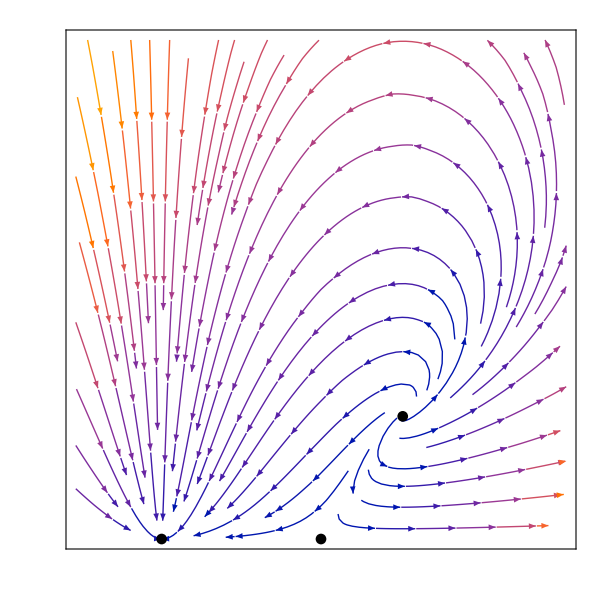

```mathematica
(*Show the plots of the phase space and fixed points together*)
Show[PhaseSpacexz,FPShowxz,FrameLabel->{MaTeX["x",FontSize->18],MaTeX["z",FontSize->18]},FrameTicks->{{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->18]},{z,0.5Range[-1,6]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,1Range[-1,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{-1,5},{0,3}},ImageSize->{600,600},PlotRangePadding->{0.08,0.08}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.0125 (6.+37. x+60. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11617,z→0.7375},{x→3.,y→1.11617,z→0.7375}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5375+1.5 x-1. z) | 0.075+0.75 x^2-1. x (1.5375+z) | -x y
0.0770833+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.0125 (6.+37. x+60. x^2)) | (0. | 0.075-1.6125 x+0.2875 x^2-0.75 x^3 | 0.
0.0770833+0.25 x | 0. | -1/6
0. | -0.225-1.3125 x-1.7875 x^2+0.75 x^3 | 0.) | (0
-√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)
√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)) | (0.666667/(0.308333+1. x) | 0 | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | -(1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | (1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.188808 | 0. | 0.00645497
0.0895833 | 0.258199 | -1/6
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0201538 | -0.800065 | 0.599574
0. | 1. | 0.
0.612372 | -0.790569 | 0.)
(0.05
0.129099
0.) | (-0.188808 | 0. | -0.00645497
0.0895833 | -0.258199 | -1/6
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0201538 | 0.800065 | 0.599574
0. | 1. | 0.
0.612372 | 0.790569 | 0.)
(2.
-0.816497
0.) | (-1.19413 | 0. | 1.63299
0.577083 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.605959 | -0.275985 | 0.746087)
(2.
0.816497
0.) | (1.19413 | 0. | -1.63299
0.577083 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.605959 | 0.275985 | 0.746087)
(3.
-1.11617
0.7375) | (-2.48348 | -8.88178×10^-16 | 3.34851
0.827083 | 2.23234 | -1/6
-0.823175 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | 1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | -0.180212-0.0432659 ⅈ | 0.326482+0.289752 ⅈ
0.880401+0. ⅈ | -0.180212+0.0432659 ⅈ | 0.326482-0.289752 ⅈ)
(3.
1.11617
0.7375) | (2.48348 | -8.88178×10^-16 | -3.34851
0.827083 | -2.23234 | -1/6
0.823175 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | -1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | 0.180212-0.0432659 ⅈ | 0.326482-0.289752 ⅈ
0.880401+0. ⅈ | 0.180212+0.0432659 ⅈ | 0.326482+0.289752 ⅈ)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLine=ParametricPlot3D[{FP[1][[1]],FP[1][[2]],FP[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyz=ListPointPlot3D[Table[FP[i],{i,2,7}],PlotStyle->Black];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyz=StreamPlot3D[{de1,de2,de3},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and the fixed points together*)
Show[PhaseSpacexyz,FPsxyz,EinsteinPointLine]
```

-Graphics3D-

### Compactification

#### Compact x - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→0.047619,Z→0.},{X→0.666667,Z→0.},{X→0.75,Z→0.42446}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((1.6875-0.6875 Z+X (-4.725+2.725 Z))/(-1.+Z) | ((-1+X) X)/(-1+Z)^2
-((-1+Z) Z)/(-1+X)^2 | ((-3+4 X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.047619
0.) | (-1.4625 | -0.0453515
0. | -2.95) | (-2.95
-1.4625) | (0.0304742 | 0.999536
1. | 0.)
(0.666667
0.) | (1.4625 | -0.222222
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.0898773 | 0.995953)
(0.75
0.42446) | (2.225 | -0.566045
3.9087 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.266011+0.236084 ⅈ | 0.934613+0. ⅈ
0.266011-0.236084 ⅈ | 0.934613+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShowCompactxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpaceCompactxz=StreamPlot[{deX,deZ},{X,-0.1,1},{Z,0,1},FrameLabel->{"X","Z"}];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLine=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)==0,{X,0,1},{Z,0,1},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where X' = 0*)
XLine=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{X,0,1},{Z,-0.1,1},ContourStyle->Red,PlotPoints->100];
```

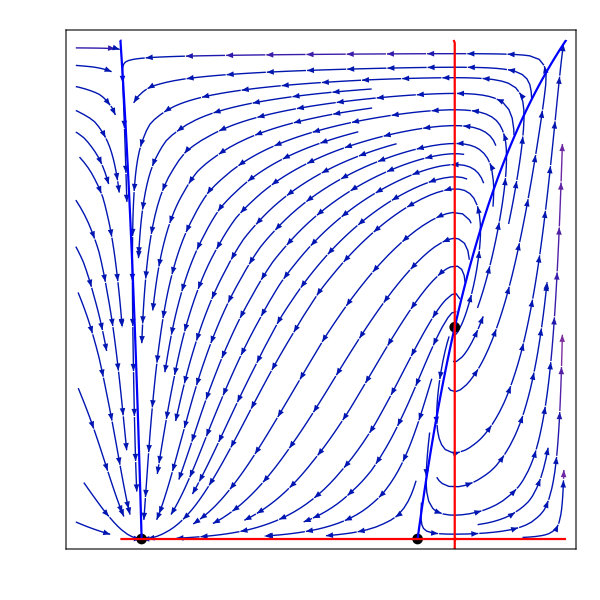

```mathematica
(*Show the phase space, fixed points and Z' = 0 and X' = 0 curves together*)
Show[PhaseSpaceCompactxz,FPShowCompactxz,ZLine,XLine,FrameLabel->{MaTeX["X",FontSize->18],MaTeX["Z",FontSize->18]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->18]},{X,0.2Range[-1,5]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[0,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{-.1,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

```mathematica
(*Evaluate X' at X = 0*)
(*X'(X = 0) > 0, therefore trajectories that are initially to the right of the X' = 0 curve will always satisy X > 0*)
deX/.X->0
```

0.075

#### Compact X - Y - Z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[5]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[6]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[7]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[8]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShowXYZ=ListPointPlot3D[Table[FP[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Plot the extra fixed points from compactification*)
CompactFPShow=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineXYZ=ParametricPlot3D[{FP[1][[1]],FP[1][[2]],FP[1][[3]]},{X,0,1},{Z,0,1},PlotStyle->Directive[Red,Thickness[.01]]];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpaceXYZ=StreamPlot3D[{deX,deY,deZ},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"}];
```

Min::nord: Invalid comparison with -1.57596-2.32827×10^-7 ⅈ attempted.

Max::nord: Invalid comparison with -1.57596-2.32827×10^-7 ⅈ attempted.

Min::nord: Invalid comparison with -1.52559+8.15036×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with -1.52559+8.15036×10^-9 ⅈ attempted.

Min::nord: Invalid comparison with -1.44197+9.85289×10^-8 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -1.44197+9.85289×10^-8 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*Show the phase space and fixed points together*)
Show[PhaseSpaceXYZ,FPShowXYZ,CompactFPShow,EinsteinPointLineXYZ]
```

-Graphics3D-

## Constant Curvature Hypersurfaces

## Set-up for x-Y-Z Phase Spaces

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the initial conditions for x0, y0 and a0*)
x0=ℛ/α;
a0=1;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[5]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[6]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[7]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[8]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShowXYZ=ListPointPlot3D[Table[FP[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Plot the extra fixed points from compactification*)
CompactFPShowXYZ=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
(*deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deat:=a1'[t]==a1[t]*(Y1[t]/((1-Y1[t]^2)^(1/2)))*)
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deXt:=X1'[t]==-3*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])
deat:=a1'[t]==a1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
trajConstantK[K_,Z0_,β_]=NDSolve[{deXt,deZt,deat,X1[0]==x0/(1+x0),Z1[0]==Z0,a1[0]==a0}, {X1,Z1,a1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition Z0 is not a number or a rectangular array of numbers.

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
(*trajConstantK[K_,Z0_,β_]=NDSolve[{deXt,deYt,deZt,deat,X1[0]==x0/(1+x0),Y1[0]==Re[β*y0/Sqrt[1+y0^2]],Z1[0]==Z0,a1[0]==a0}, {X1,Y1,Z1,a1},{t,-100,100}];*)
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and the scale factor, a, to solve for the Einstein fixed points*)
(*z has been substituted as z(x,a) from the Friedmann equation at an Einstein fixed point where y = 0*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*((-x1[t]+3*K/a1[t]^2))
deat:=a1'[t]==a1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajK[K_]=NDSolve[{dext,deat,x1[0]==x0,a1[0]==a0},{x1,a1},{t,-100,100}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t])-((3 K)/a1[t]^2-x1[t]) x1[t],a1'[t]==a1[t],x1[0]==0.1,a1[0]==1},{x1,a1},{t,-100,100}]

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and the scale factor, a*)
deXtXZa:=X1'[t]==-3*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))
deZtXZa:=Z1'[t]==-3*Z1[t]*(1-Z1[t])+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])
deatXZa:=a1'[t]==a1[t]
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
ffsConstantK[X_,Z_]=X/(3*(1-X))+Z/(3*(1-Z));
```

```mathematica
(*Rearrange the FFS for Y*)
(*Note that when plotting the FFS, +FFSSubMan and -FFSSubMan needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFSConstantK[X_,Z_]=Sqrt[ffsConstantK[X,Z]/(1+ffsConstantK[X,Z])];
```

```mathematica
(*Plot the FFS*)
ConstantKFFS=ParametricPlot3D[{{X,FFSConstantK[X,Z],Z},{X,-FFSConstantK[X,Z],Z}},{X,0,1},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008],Opacity[0.3]}},PlotPoints->100,PlotRange->All,Mesh->None];
```

## Case 1: Limiting Case

#### Find the Limiting Cases

```mathematica
(*Clear the value of K*)
Clear[K,KLimiting]
```

```mathematica
(*Define a constant K*)
(*KLimiting=0.03572*)
KLimiting=0.02
```

0.02

```mathematica
z0KLimiting=-x0+3*KLimiting/(a0^2)
```

-0.04

```mathematica
Z0KLimiting=z0KLimiting/(1+z0KLimiting)
```

-0.0416667

```mathematica
solLimiting=trajConstantK[KLimiting,Z0KLimiting,1]
```

NDSolve::ndsz: At t == -1.1299, step size is effectively zero; singularity or stiff system suspected.

{{X1→InterpolatingFunction[…],Z1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Solve for a fixed K value*)
(*solLimiting=trajK[KLimiting]*)
```

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableKLimiting=Table[Re[X1[i]]/.solLimiting,{i,-1.12,5,.001}];
ZTableKLimiting=Table[Re[Z1[i]]/.solLimiting,{i,-1.12,5,.001}];
aTableKLimiting=Table[Re[a1[i]]/.solLimiting,{i,-1.12,5,.001}];
```

```mathematica
(*Using the values of x and a found numerically, solve the equation to find the Einstein fixed points*)
(*EinsteinPlotValuesKLimiting=(ZTableKLimiting/(1-ZTableKLimiting))+(XTableKLimiting/(1-XTableKLimiting))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableKLimiting/(1-XTableKLimiting))^2;*)

EinsteinPlotValuesKLimiting=(-(XTableKLimiting/(1-XTableKLimiting))+3*KLimiting/(aTableKLimiting^2))+(XTableKLimiting/(1-XTableKLimiting))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableKLimiting/(1-XTableKLimiting))^2;
```

```mathematica
CompactEinsteinPlotValuesKLimiting=EinsteinPlotValuesKLimiting/Sqrt[1+(EinsteinPlotValuesKLimiting)^2];
```

```mathematica
(*Find the maximum value of CompactEinsteinPlotValuesKLimitingFull*)
(*A limiting case exists when MaxValue = 0*)
MaxPoint=Max[CompactEinsteinPlotValuesKLimiting]
```

0.167552

```mathematica
(*Find the position of the value closest to zero in the array*)
PositionNearestToZeroKLimiting=Flatten[Position[CompactEinsteinPlotValuesKLimiting,MaxPoint]][[1]]
```

1

```mathematica
(*Find the corresponding x and a values to find the Einstein point*)
EinsteinPointLimitingKSol=Flatten[{XTableKLimiting[[PositionNearestToZeroKLimiting]],0,ZTableKLimiting[[PositionNearestToZeroKLimiting]]}]
```

{0.165144,0,-35.5612}

```mathematica
(*Calculate the value of z at the Einstein fixed point using the Friedmann equation*)
(*zEinsteinPointLimitingK=-EinsteinPointLimitingKSol[[1]]+3*(KLimiting)/(EinsteinPointLimitingKSol[[2]]^2)*)
```

```mathematica
(*Express the Einstein fixed point in terms of the compactified variables X-Y-Z*)
(*EinsteinPointLimitingK=Flatten[{EinsteinPointLimitingKSol[[1]]/(1+EinsteinPointLimitingKSol[[1]]),0,zEinsteinPointLimitingK/(1+zEinsteinPointLimitingK)}]*)
```

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableKLimitingFull=Table[Re[X1[i]]/.solLimiting,{i,-1.12,100,.1}];
ZTableKLimitingFull=Table[Re[Z1[i]]/.solLimiting,{i,-1.12,100,.1}];
aTableKLimitingFull=Table[Re[a1[i]]/.solLimiting,{i,-1.12,100,.1}];
```

```mathematica
EinsteinPlotValuesKLimitingFull=(-(XTableKLimitingFull/(1-XTableKLimitingFull))+3*KLimiting/(aTableKLimitingFull^2))+(XTableKLimitingFull/(1-XTableKLimitingFull))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableKLimitingFull/(1-XTableKLimitingFull))^2;
```

```mathematica
(*EinsteinPlotValuesKLimitingFull=(ZTableKLimitingFull/(1-ZTableKLimitingFull))+(XTableKLimitingFull/(1-XTableKLimitingFull))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableKLimitingFull/(1-XTableKLimitingFull))^2;*)
```

```mathematica
(*Using the values of x and a found numerically, solve the equation to find the Einstein fixed points*)
(*EinsteinPlotValuesKLimitingFull=(ZTableKLimitingFull/(1-ZTableKLimitingFull))+(XTableKLimitingFull/(1-XTableKLimitingFull))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableKLimitingFull/(1-XTableKLimitingFull))^2;*)
```

```mathematica
CompactEinsteinPlotValuesKLimitingFull=EinsteinPlotValuesKLimitingFull/Sqrt[1+EinsteinPlotValuesKLimitingFull^2];
```

```mathematica
(*Merge the xTable values and the CompactEinsteinPlotValues values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsKLimitingFull=MapThread[h,{XTableKLimitingFull,CompactEinsteinPlotValuesKLimitingFull}];
```

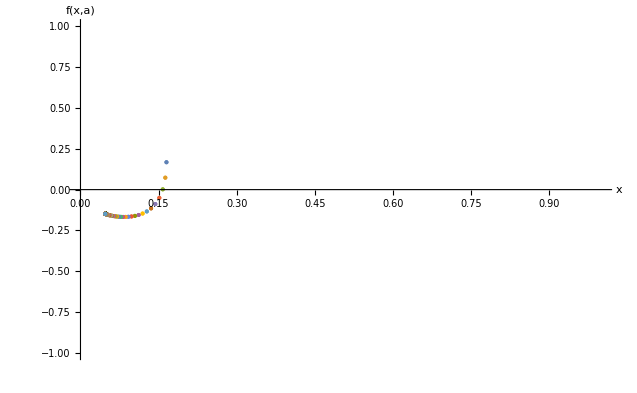

```mathematica
(*Plot the solution*)
EinsteinPlotKLimiting=ListPlot[EinsteinPointSolutionsKLimitingFull,AxesLabel->{"x","f(x,a)"},PlotRange->{{0,1},{-1,1}}]
```

#### 3-D x-Y-Z Phase Space

```mathematica
trajConstantK[KLimiting,Z0KLimiting,1]
```

```mathematica
Sqrt[X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)]/Sqrt[1+X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)]
```

```mathematica
(*Plot trajectories for a range of intial Z0 values*)
```

```mathematica
PhaseSpaceConstantKLimiting[1]=Table[ParametricPlot3D[Evaluate[{X1[t],Sqrt[X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)]/Sqrt[1+X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)],Z1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0,0.01,.001}];
```

```mathematica
PhaseSpaceConstantKLimiting[2]=Table[ParametricPlot3D[Evaluate[{X1[t],Sqrt[X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)]/Sqrt[1+X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)],Z1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.03,.005}];
```

```mathematica
PhaseSpaceConstantKLimiting[3]=Table[ParametricPlot3D[Evaluate[{X1[t],Sqrt[X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)]/Sqrt[1+X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)],Z1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.03,0.09,.02}];
```

```mathematica
PhaseSpaceConstantKLimiting[4]=Table[ParametricPlot3D[Evaluate[{X1[t],Sqrt[X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)]/Sqrt[1+X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-3*KLimiting/(a1[t]^2)],Z1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.99,.1}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKLimitingPlots=Table[PhaseSpaceConstantKLimiting[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinPointsKLimiting=ListPointPlot3D[{EinsteinPointLimitingKSol},PlotStyle->Black];
```

```mathematica
(*Plot the Y = 0 line*)
Y0KLimiting=ParametricPlot3D[Evaluate[{X1[t],0,Z1[t]}/.trajConstantK[KLimiting,Z0KLimiting,1]],{t,-12.9,100},AxesLabel->{"X","Y","Z"},PlotRange->{{0,1},{-1,1},{0,1}},PlotPoints->500];
```

```mathematica
(*Plot the Closed Friedmann Separatrix (CFS)*)
(*Numerically solve the system of equations using the Einstein fixed point as the initial conditions*)
trajKLimitingCFS=NDSolve[{deXtXZa,deZtXZa,deatXZa,X1[0]==EinsteinPointLimitingK[[1]],Z1[0]==EinsteinPointLimitingK[[3]],a1[0]==EinsteinPointLimitingKSol[[2]]},{X1,Z1,a1},{t,-100,100}]
```

Part::partd: Part specification EinsteinPointLimitingK⟦1⟧ is longer than depth of object.

Part::partd: Part specification EinsteinPointLimitingK⟦3⟧ is longer than depth of object.

NDSolve::ndinnt: Initial condition EinsteinPointLimitingK⟦1⟧ is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t])-((1-X1[t]) X1[t] Z1[t])/(1-Z1[t]),Z1'[t]==-3 (1-Z1[t]) Z1[t]+(X1[t] (1-Z1[t]) Z1[t])/(1-X1[t]),a1'[t]==a1[t],X1[0]==EinsteinPointLimitingK⟦1⟧,Z1[0]==EinsteinPointLimitingK⟦3⟧,a1[0]==0},{X1,Z1,a1},{t,-100,100}]

```mathematica
(*Define the CFS in terms of Y*)
CFSKLimiting=ParametricPlot3D[Evaluate[{{X1[t],Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))],Z1[t]},{X1[t],-Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))],Z1[t]}}/.trajConstantK[KLimiting,Z0KLimiting,1]],{t,-100,100},AxesLabel->{"X","Y","Z"},PlotRange->{{0,1},{-1,1},{0,1}},PlotStyle->Black];
```

```mathematica
trajConstantKXZ[KLimiting,Z0KLimiting,1]
```

trajConstantKXZ[0.0357,0.00704995,1]

```mathematica
trajConstantK[KLimiting,Z0KLimiting,1]
```

{{X1→InterpolatingFunction[…],Z1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
Z0KLimiting
```

0.00704995

```mathematica
(*Show all components of the phase space*)
KLimitingPlot=Show[trajConstantKLimitingPlots,EinsteinPointsKLimiting,Y0KLimiting,CFSKLimiting,FPShowXYZ,CompactFPShowXYZ,AccnXYZ,AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},PlotRange->{{0,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

#### 2-D x-Y Projection

```mathematica
(*Plot the trajectories defined above on the X-Y plane*)
```

```mathematica
PhaseSpaceConstantKLimitingProjection[1]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0,0.01,.001}];
```

```mathematica
PhaseSpaceConstantKLimitingProjection[2]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.03,.005}];
```

```mathematica
PhaseSpaceConstantKLimitingProjection[3]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.03,0.09,.02}];
```

```mathematica
PhaseSpaceConstantKLimitingProjection[4]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KLimiting,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.09,0.99,.1}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKLimitingPlotsProjection=Table[PhaseSpaceConstantKLimitingProjection[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinPointsKLimitingProjection=ListPlot[{{EinsteinPointLimitingKSol[[1]],EinsteinPointLimitingKSol[[2]]}},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSKLimitingProjection=ParametricPlot[Evaluate[{{X1[t],Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))]},{X1[t],-Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KLimiting/(a1[t]^2))]}}/.trajKLimitingCFS],{t,-100,100},AxesLabel->{"X","Y","Z"},PlotRange->Full,PlotStyle->Black,PlotPoints->10000];
```

NDSolve::ndinnt: Initial condition EinsteinPointLimitingK⟦1⟧ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{X1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+X1[«1»])-((1+Times[«2»]) X1[t] Z1[t])/Plus[«2»],Z1'[t]==-3 (1+Times[«2»]) Z1[t]+(X1[t] (1+Times[«2»]) Z1[t])/Plus[«2»],a1'[t]==a1[t],X1[0]==EinsteinPointLimitingK⟦1⟧,Z1[0]==EinsteinPointLimitingK⟦3⟧,a1[0]==0},{X1,Z1,a1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -100. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -100. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{X1'[-100.]==-3. (Times[«2»]+Times[«2»]) (Times[«2»]+X1[«1»])-(1. (1.+Times[«2»]) X1[-100.] Z1[-100.])/Plus[«2»],Z1'[-100.]==-3. (1.+Times[«2»]) Z1[-100.]+(X1[-100.] (1.+Times[«2»]) Z1[-100.])/Plus[«2»],a1'[-100.]==a1[-100.],X1[0.]==«22»⟦1⟧,Z1[0.]==EinsteinPointLimitingK⟦3⟧,a1[0.]==0.},{«1»},{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -99.98 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

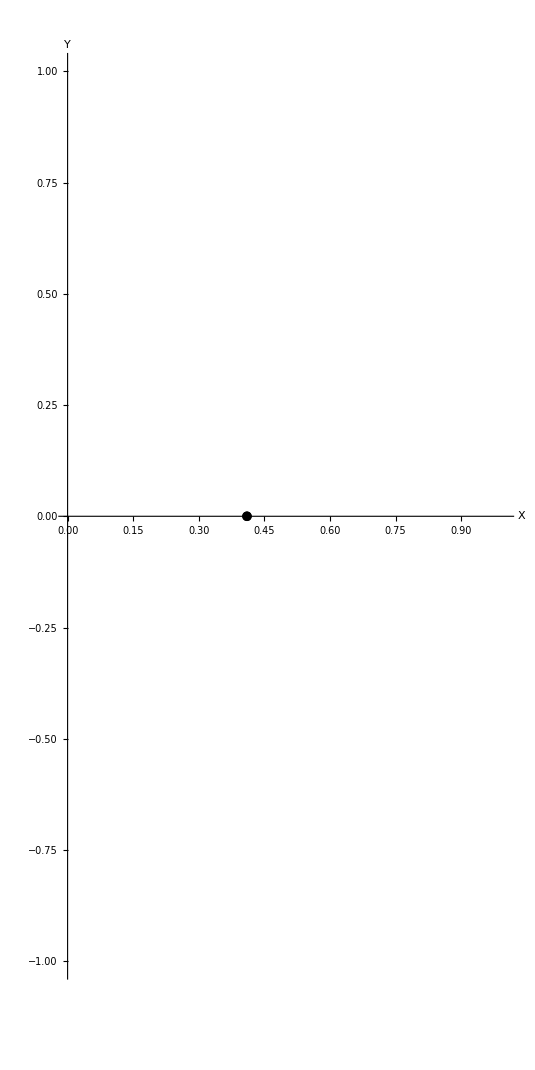

```mathematica
(*Show all the trajectories on the same plot*)
KLimitingPlotProjection=Show[trajConstantKLimitingPlotsProjection,EinsteinPointsKLimitingProjection,CFSKLimitingProjection,PlotRange->{{0,1},{-1,1}}]
```

## Case 2 : 2 Einstein Fixed Points

#### Numerically find the Einstein Fixed Points

```mathematica
(*Clear the value of K*)
Clear[K]
```

```mathematica
(*Define a constant K > KLimiting*)
KClosed=0.02;
```

```mathematica
(*Solve for a fixed K value*)
solClosed=trajK[KClosed]
```

NDSolve::ndcf: Repeated convergence test failure at t == -12.9302; unable to continue.

{{x1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Define a reduced array to find the first Einstein point around x = ℛ*)
xTableKClosedSol1=Table[Re[x1[i]]/.solClosed,{i,-1.3,5,.001}];
aTableKClosedSol1=Table[Re[a1[i]]/.solClosed,{i,-1.3,5,.001}];
```

```mathematica
(*Using the reduced arrays of x and a found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesKClosedSol1[K_]=((-xTableKClosedSol1+3*K/(aTableKClosedSol1^2))+(xTableKClosedSol1)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableKClosedSol1)^2);
```

```mathematica
(*Find the value closest to zero in the array to find the Einstein points closest to x = ℛ*)
NearestToZeroKClosed1=Flatten[Nearest[EinsteinPlotValuesKClosedSol1[KClosed],0]]
```

{0.000172684}

```mathematica
(*Find the position of the values closest to zero in the array*)
PositionNearestToZeroKClosed1=Flatten[Position[EinsteinPlotValuesKClosedSol1[KClosed],NearestToZeroKClosed1]]
```

{137}

```mathematica
(*Find the corresponding x and a values to find the Einstein points*)
EinsteinPointClosedKSol1ax=Flatten[{xTableKClosedSol1[[PositionNearestToZeroKClosed1]],aTableKClosedSol1[[PositionNearestToZeroKClosed1]]}]
```

{0.317667,0.312235}

```mathematica
(*Calculate the value of z at the Einstein fixed point using the Friedmann equation*)
zEinsteinPointClosedKSol1=-EinsteinPointClosedKSol1ax[[1]]+3*(KClosed)/(EinsteinPointClosedKSol1ax[[2]]^2)
```

0.297778

```mathematica
(*Express the Einstein fixed points in terms of the compactified variables X-Y-Z*)
EinsteinPointClosedKSol1=Flatten[{EinsteinPointClosedKSol1ax[[1]]/(1+EinsteinPointClosedKSol1ax[[1]]),0,zEinsteinPointClosedKSol1/(1+zEinsteinPointClosedKSol1)}]
```

{0.241083,0,0.229452}

```mathematica
(*Define a reduced array to find the second Einstein point*)
xTableKClosedSol2=Table[Re[x1[i]]/.solClosed,{i,-2,-1.5,.00001}];
aTableKClosedSol2=Table[Re[a1[i]]/.solClosed,{i,-2,-1.5,.00001}];
```

```mathematica
(*Using the reduced arrays of x and a found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesKClosedSol2[K_]=((-xTableKClosedSol2+3*K/(aTableKClosedSol2^2))+(xTableKClosedSol2)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableKClosedSol2)^2);
```

```mathematica
(*Find the value closest to zero in the array to find the remaining Einstein points*)
NearestToZeroKClosed2=Flatten[Nearest[EinsteinPlotValuesKClosedSol2[KClosed],0]]
```

{3.40986×10^-6}

```mathematica
(*Find the position of the value closest to zero in the array*)
PositionNearestToZeroKClosed2=Flatten[Position[EinsteinPlotValuesKClosedSol2[KClosed],NearestToZeroKClosed2]]
```

{10949}

```mathematica
(*Find the corresponding x and a values to find the Einstein points*)
EinsteinPointClosedKSol2=Flatten[{xTableKClosedSol2[[PositionNearestToZeroKClosed2]],aTableKClosedSol2[[PositionNearestToZeroKClosed2]]}]
```

{1.11295,0.150993}

```mathematica
(*Calculate the value of z at the Einstein fixed point using the Friedmann equation*)
zEinsteinPointClosedKSol2=-EinsteinPointClosedKSol2[[1]]+3*(KClosed)/(EinsteinPointClosedKSol2[[2]]^2)
```

1.51874

```mathematica
(*Express the Einstein fixed points in terms of the compactified variables X-Y-Z*)
EinsteinPointClosedKSol2=Flatten[{EinsteinPointClosedKSol2[[1]]/(1+EinsteinPointClosedKSol2[[1]]),0,zEinsteinPointClosedKSol2/(1+zEinsteinPointClosedKSol2)}]
```

{0.526729,0,0.602977}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableKClosedFull=Table[Re[x1[i]]/.solClosed,{i,-13.7,100,.1}];
aTableKClosedFull=Table[Re[a1[i]]/.solClosed,{i,-13.7,100,.1}];
```

InterpolatingFunction::dmval: Input value {-13.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-13.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-13.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-13.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-13.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-13.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Using the values of x and a found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesKClosedFull[K_]=((-xTableKClosedFull+3*K/(aTableKClosedFull^2))+(xTableKClosedFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableKClosedFull)^2);
```

```mathematica
(*Define compactified tables*)
XTableKClosedFull=(xTableKClosedFull)/(1+xTableKClosedFull);
CompactEinsteinPlotValuesKClosedFull=EinsteinPlotValuesKClosedFull[KClosed]/Sqrt[1+(EinsteinPlotValuesKClosedFull[KClosed])^2];
```

```mathematica
(*Merge the xTable values and the CompactEinsteinPlotValues values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsKClosedFull=MapThread[h,{XTableKClosedFull,CompactEinsteinPlotValuesKClosedFull}];
```

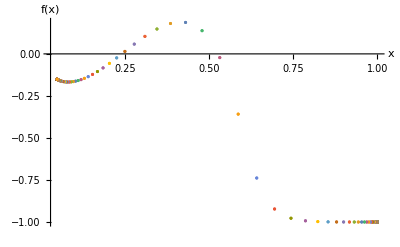

```mathematica
(*Plot the solution*)
EinsteinPlotKClosed=ListPlot[EinsteinPointSolutionsKClosedFull,AxesLabel->{"x","f(x)"},PlotRange->Full]
```

#### 3-D x-Y-Z Phase Space

```mathematica
(*Plot trajectories for a range of intial Z0 values*)
```

```mathematica
PhaseSpaceConstantKClosed[1]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}],{Z0,0,0.01,.001}];
```

```mathematica
PhaseSpaceConstantKClosed[2]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.02,.002}];
```

```mathematica
PhaseSpaceConstantKClosed[3]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.02,0.04,.01}];
```

```mathematica
PhaseSpaceConstantKClosed[4]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.04,0.99,.1}];
```

```mathematica
(*Define intial conditions for a cyclic trajectory*)
XCyclic=.52;
ZCyclic=.6;
YCyclic=0.15;
aCyclic=Sqrt[3*KClosed/((XCyclic/(1+XCyclic))+(ZCyclic/(1+ZCyclic))-3*YCyclic^2/(1-YCyclic^2))]
```

0.304278

```mathematica
(*Solve for cyclic initial conditions*)
trajKClosedCyclic=NDSolve[{deXt,deYt,deZt,deat,X1[0]==XCyclic,Y1[0]==YCyclic,Z1[0]==ZCyclic,a1[0]==aCyclic},{X1,Y1,Z1,a1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Plot the cyclic trajectory*)
PhaseSpaceConstantKClosed[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]}}/.trajKClosedCyclic],{t,-100,99},AxesLabel->{"X","Y","Z"},PlotRange->{{0,1},{-1,1},{0,1}},PlotPoints->500,PlotStyle->{{Gray,Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKClosedPlots=Table[PhaseSpaceConstantKClosed[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinPlotKClosed=ListPointPlot3D[{{EinsteinPointClosedKSol1},{EinsteinPointClosedKSol2}},PlotStyle->Black];
```

```mathematica
(*Plot the Y = 0 line*)
Y0KClosed=ParametricPlot3D[Evaluate[{x1[t]/(1+x1[t]),0,(3*KClosed/(a1[t]^2)-x1[t])/(1+(3*KClosed/(a1[t]^2)-x1[t]))}/.trajK[KClosed]],{t,-13.8,100},AxesLabel->{"X","Y","Z"},PlotRange->{{0,1},{-1,1},{0,1}},PlotPoints->500];
```

NDSolve::ndcf: Repeated convergence test failure at t == -12.9302; unable to continue.

InterpolatingFunction::dmval: Input value {-13.7998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Plot the Closed Friedmann Separatrix (CFS)*)
(*Numerically solve the system of equations using the Einstein fixed point as the initial conditions*)
trajKClosedCFS=NDSolve[{deXtXZa,deZtXZa,deatXZa,X1[0]==EinsteinPointClosedKSol1[[1]],Z1[0]==EinsteinPointClosedKSol1[[3]],a1[0]==EinsteinPointClosedKSol1ax[[2]]},{X1,Z1,a1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Z1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Define the CFS in terms of Y*)
CFSKClosed=ParametricPlot3D[Evaluate[{{X1[t],Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))],Z1[t]},{X1[t],-Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))],Z1[t]}}/.trajKClosedCFS],{t,-100,100},AxesLabel->{"X","Y","Z"},PlotRange->Full,PlotStyle->Black,PlotPoints->10000];
```

```mathematica
(*Show all components of the phase space together*)
Show[trajConstantKClosedPlots,EinsteinPlotKClosed,Y0KClosed,CFSKClosed,FPShowXYZ,CompactFPShowXYZ,AccnXYZ,AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},PlotRange->{{0,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

#### 2-D x-Y Projection

```mathematica
(*Plot the trajectories defined above on the X-Y plane*)
```

```mathematica
PhaseSpaceConstantKClosedProjection[1]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0,0.01,.001}];
```

```mathematica
PhaseSpaceConstantKClosedProjection[2]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.02,.002}];
```

```mathematica
PhaseSpaceConstantKClosedProjection[3]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.02,0.04,.01}];
```

```mathematica
PhaseSpaceConstantKClosedProjection[4]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosed,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.04,0.99,.1}];
```

```mathematica
trajKClosedCyclic=NDSolve[{deXt,deYt,deZt,deat,X1[0]==XCyclic,Y1[0]==YCyclic,Z1[0]==ZCyclic,a1[0]==aCyclic},{X1,Y1,Z1,a1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
XCyclic=.52;
ZCyclic=.6;
YCyclic=0.1947;
aCyclic=Sqrt[3*KClosed/((XCyclic/(1+XCyclic))+(ZCyclic/(1+ZCyclic))-3*YCyclic^2/(1-YCyclic^2))]
```

0.316518

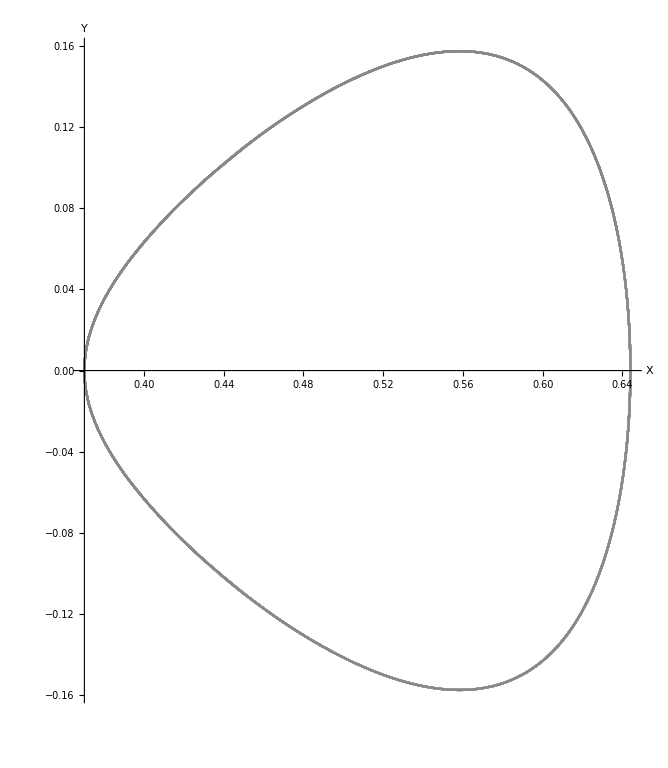

```mathematica
(*Plot the cyclic trajectory*)
PhaseSpaceConstantKClosedProjection[5]=ParametricPlot[Evaluate[{{X1[t],Y1[t]}}/.trajKClosedCyclic],{t,-100,100},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotStyle->{{Gray,Opacity[0.75]}}]
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKClosedPlotsProjection=Table[PhaseSpaceConstantKClosedProjection[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinPointsKClosedProjection=ListPlot[{{EinsteinPointClosedKSol1[[1]],EinsteinPointClosedKSol1[[2]]},{EinsteinPointClosedKSol2[[1]],EinsteinPointClosedKSol2[[2]]}},PlotStyle->Black];
```

```mathematica
(*Define the CFS in terms of Y*)
CFSKClosedProjection=ParametricPlot[Evaluate[{{X1[t],Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))]},{X1[t],-Sqrt[(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))]/Sqrt[1+(X1[t]/(3*(1-X1[t]))+Z1[t]/(3*(1-Z1[t]))-KClosed/(a1[t]^2))]}}/.trajKClosedCFS],{t,-100,100},AxesLabel->{"X","Y","Z"},PlotRange->Full,PlotStyle->Black,PlotPoints->10000];
```

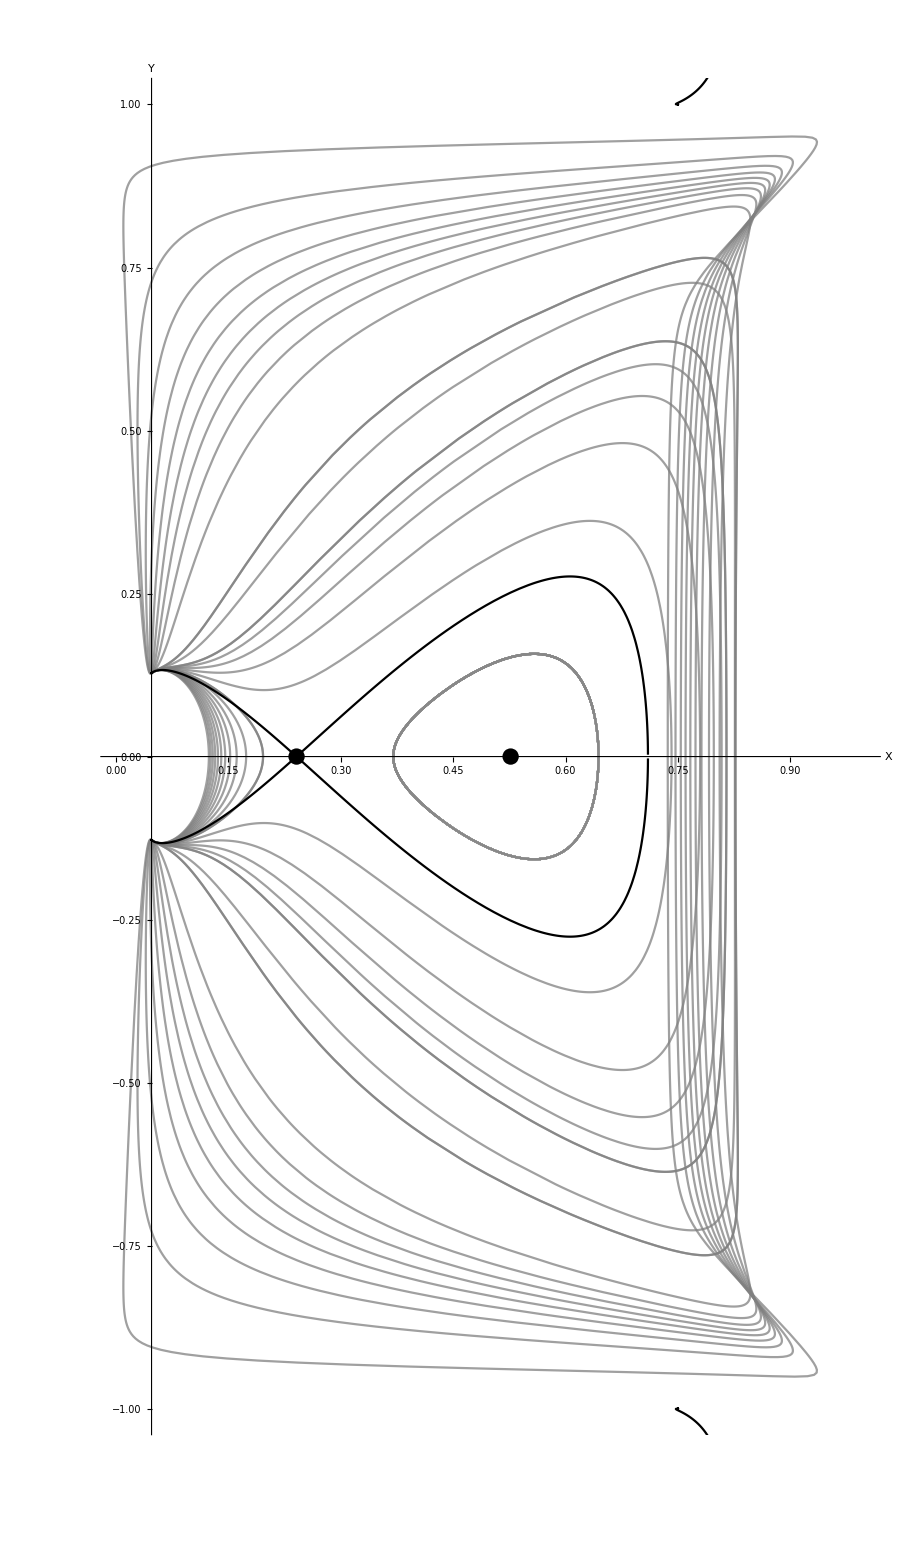

```mathematica
(*Show all the trajectories on the same plot*)
KClosedPlotProjection=Show[trajConstantKClosedPlotsProjection,EinsteinPointsKClosedProjection,CFSKClosedProjection,PlotRange->{{0,1},{-1,1}}]
```

## Case 3 : No Einstein Fixed Points

### Case 3 i : Closed Case

#### Show that there are no Einstein fixed points

```mathematica
(*Clear the value of K*)
Clear[K]
```

```mathematica
(*Define a constant 0 < K < KLimiting*)
KClosedNoEPts=0.009;
```

```mathematica
(*Solve trajK for K = 0*)
solClosedNoEPts=trajK[KClosedNoEPts]
```

NDSolve::ndcf: Repeated convergence test failure at t == -13.1993; unable to continue.

{{x1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableKClosedNoEPtsFull=Table[Re[x1[i]]/.solClosedNoEPts,{i,-13.1,100,.1}];
aTableKClosedNoEPtsFull=Table[Re[a1[i]]/.solClosedNoEPts,{i,-13.1,100,.1}];
```

```mathematica
(*Using the values of x and a found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesKClosedNoEPtsFull[K_]=((-xTableKClosedNoEPtsFull+3*K/(aTableKClosedNoEPtsFull^2))+(xTableKClosedNoEPtsFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableKClosedNoEPtsFull)^2);
```

```mathematica
(*Define compactified tables*)
XTableKClosedNoEPtsFull=(xTableKClosedNoEPtsFull)/(1+xTableKClosedNoEPtsFull);
CompactEinsteinPlotValuesKClosedNoEPtsFull=EinsteinPlotValuesKClosedNoEPtsFull[KClosedNoEPts]/Sqrt[1+(EinsteinPlotValuesKClosedNoEPtsFull[KClosedNoEPts])^2];
```

```mathematica
(*Merge the xTable values and the CompactEinsteinPlotValues values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsKClosedNoEPtsFull=MapThread[h,{XTableKClosedNoEPtsFull,CompactEinsteinPlotValuesKClosedNoEPtsFull}];
```

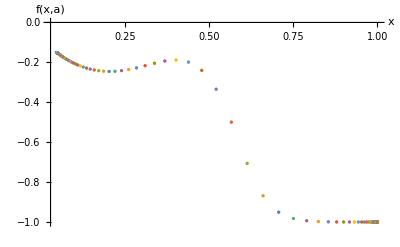

```mathematica
(*Plot the solution*)
EinsteinPlotKClosedNoEPts=ListPlot[EinsteinPointSolutionsKClosedNoEPtsFull,AxesLabel->{"x","f(x,a)"},PlotRange->Full]
```

#### 3-D x-Y-Z Phase Space

```mathematica
(*Plot trajectories for a range of intial Z0 values*)
```

```mathematica
PhaseSpaceConstantKClosedNoEPts[1]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0,0.01,.001}];
```

```mathematica
PhaseSpaceConstantKClosedNoEPts[2]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.03,.005}];
```

```mathematica
PhaseSpaceConstantKClosedNoEPts[3]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.03,0.09,.02}];
```

```mathematica
PhaseSpaceConstantKClosedNoEPts[4]=Table[ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.99,.1}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKClosedNoEPtsPlots=Table[PhaseSpaceConstantKClosedNoEPts[i],{i,1,4}];
```

```mathematica
(*Plot the Y = 0 line*)
Y0KClosedNoEPts=ParametricPlot3D[Evaluate[{x1[t]/(1+x1[t]),0,(3*KClosedNoEPts/(a1[t]^2)-x1[t])/(1+(3*KClosedNoEPts/(a1[t]^2)-x1[t]))}/.trajK[KClosedNoEPts]],{t,-13.1,100},AxesLabel->{"X","Y","Z"},PlotRange->{{0,1},{-1,1},{0,1}},PlotPoints->500];
```

NDSolve::ndcf: Repeated convergence test failure at t == -13.1993; unable to continue.

```mathematica
(*Show all components of the phase space*)
KClosedNoEPtsPlot=Show[trajConstantKClosedNoEPtsPlots,Y0KClosedNoEPts,FPShowXYZ,CompactFPShowXYZ,AccnXYZ,AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},PlotRange->{{0,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

#### 2-D x-Y Projection

```mathematica
(*Plot the trajectories defined above on the X-Y plane*)
```

```mathematica
PhaseSpaceConstantKClosedNoEPtsProjection[1]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0,0.01,.001}];
```

```mathematica
PhaseSpaceConstantKClosedNoEPtsProjection[2]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.03,.005}];
```

```mathematica
PhaseSpaceConstantKClosedNoEPtsProjection[3]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.03,0.09,.02}];
```

```mathematica
PhaseSpaceConstantKClosedNoEPtsProjection[4]=Table[ParametricPlot[Evaluate[{X1[t],Y1[t]}/.trajConstantK[KClosedNoEPts,Z0,1]],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->All],{Z0,0.01,0.99,.1}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKClosedNoEPtsPlotsProjection=Table[PhaseSpaceConstantKClosedNoEPtsProjection[i],{i,1,4}];
```

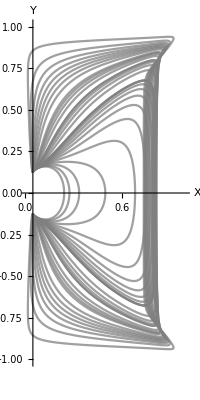

```mathematica
(*Show all the trajectories on the same plot*)
KLimitingPlotProjection=Show[trajConstantKClosedNoEPtsPlotsProjection,PlotRange->{{0,1},{-1,1}}]
```

### Case 3 ii : Flat Case

#### Show that there are no Einstein fixed points

```mathematica
(*Clear the value of K*)
Clear[K]
```

```mathematica
(*Define a constant K*)
KFlat=0;
```

```mathematica
(*Solve trajK for K = 0*)
solFlat=trajK[KFlat]
```

{{x1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableKFlatFull=Table[Re[x1[i]]/.solFlat,{i,-100,100,.1}];
aTableKFlatFull=Table[Re[a1[i]]/.solFlat,{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and a found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesKFlatFull[K_]=((-xTableKFlatFull+3*K/(aTableKFlatFull^2))+(xTableKFlatFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableKFlatFull)^2);
```

```mathematica
(*Define compactified tables*)
XTableKFlatFull=(xTableKFlatFull)/(1+xTableKFlatFull);
CompactEinsteinPlotValuesKFlatFull=EinsteinPlotValuesKFlatFull[KFlat]/Sqrt[1+(EinsteinPlotValuesKFlatFull[KFlat])^2];
```

```mathematica
(*Merge the xTable values and the CompactEinsteinPlotValues values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsKFlatFull=MapThread[h,{XTableKFlatFull,CompactEinsteinPlotValuesKFlatFull}];
```

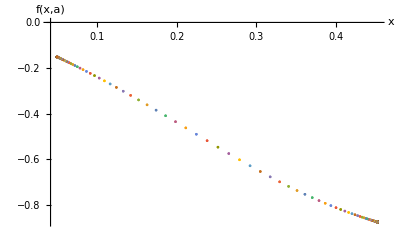

```mathematica
(*Plot the solution*)
EinsteinPlotKFlat=ListPlot[EinsteinPointSolutionsKFlatFull,AxesLabel->{"x","f(x,a)"},PlotRange->Full]
```

#### 3-D x-Y-Z Phase Space

```mathematica
(*Define K = KFlat*)
K=KFlat;
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
trajConstantKFlat[Z0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==Z0}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(0.0333333+(0.333333 Z0)/(1.-1. Z0)) β)/(√(1.03333+(0.333333 Z0)/(1.-1. Z0))) is not a number or a rectangular array of numbers.

```mathematica
(*Solve for different initial conditions*)
```

```mathematica
solKFlat[1]=trajConstantKFlat[0.01,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[2]=trajConstantKFlat[0.01,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[3]=trajConstantKFlat[0.3,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[4]=trajConstantKFlat[0.3,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[5]=trajConstantKFlat[0.5,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[6]=trajConstantKFlat[0.5,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[7]=trajConstantKFlat[0.7,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[8]=trajConstantKFlat[0.7,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[9]=trajConstantKFlat[0.8,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKFlat[10]=trajConstantKFlat[0.8,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot each trajectory*)
```

```mathematica
PhaseSpaceConstantKFlat[1]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[1],{t,-10,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[2]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[2],{t,-100,10},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[3]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[3],{t,-6,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[4]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[4],{t,-100,6},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[5]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[5],{t,-6,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[6]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[6],{t,-100,6},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[7]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[7],{t,10,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[8]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[8],{t,-100,5},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[9]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[9],{t,-5,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKFlat[10]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKFlat[10],{t,-100,5},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKFlatPlots=Table[PhaseSpaceConstantKFlat[i],{i,1,10}];
```

```mathematica
(*Show all components of the phase space*)
xYzc3=Show[trajConstantKFlatPlots,FPShowXYZ,CompactFPShowXYZ,AccnXYZ,ConstantKFFS,AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},PlotRange->{{0,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

#### 2-D x-Y Projection

```mathematica
(*Plot the trajectories defined above on the X-Y plane*)
```

```mathematica
PhaseSpaceConstantKFlatXY[1]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[1],{t,-7.5,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[2]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[2],{t,-100,7.5},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[3]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[3], {t,-6,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[4]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[4], {t,-100,6},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[5]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[5], {t,-6,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[6]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[6], {t,-100,6},PlotStyle -> {{Gray , Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[7]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[7], {t,10,100},PlotStyle -> {{Gray , Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[8]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[8], {t,-100,5},PlotStyle -> {{Gray , Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[9]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[9], {t,-5,100},PlotStyle -> {{Gray , Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
PhaseSpaceConstantKFlatXY[10]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKFlat[10], {t,-100,5},PlotStyle -> {{Gray , Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceConstantKFlatProjection=Table[PhaseSpaceConstantKFlatXY[i],{i,1,10}];
```

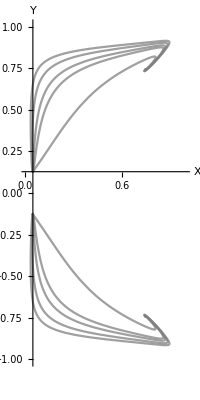

```mathematica
(*Show all the trajectories on the same plot*)
Show[PhaseSpaceConstantKFlatProjection,PlotRange->{{0,1},{-1,1}}]
```

### Case 3 iii: Open Case

#### Show that there are no Einstein fixed points

```mathematica
(*Clear the value of K*)
Clear[K]
```

```mathematica
(*Define a constant K*)
KOpen=- 0.1;
```

```mathematica
(*Solve trajK for K = 0*)
solOpen=trajK[KOpen]
```

NDSolve::nderr: Error test failure at t == -27.7967; unable to continue.

{{x1→InterpolatingFunction[…],a1→InterpolatingFunction[…]}}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableKOpenFull=Table[Re[x1[i]]/.solOpen,{i,-27.7,100,.1}];
aTableKOpenFull=Table[Re[a1[i]]/.solOpen,{i,-27.7,100,.1}];
```

```mathematica
(*Using the values of x and a found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesKOpenFull[K_]=((-xTableKOpenFull+3*K/(aTableKOpenFull^2))+(xTableKOpenFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableKOpenFull)^2);
```

```mathematica
(*Define compactified tables*)
XTableKOpenFull=(xTableKOpenFull)/(1+xTableKOpenFull);
CompactEinsteinPlotValuesKOpenFull=EinsteinPlotValuesKOpenFull[KOpen]/Sqrt[1+(EinsteinPlotValuesKOpenFull[KOpen])^2];
```

```mathematica
(*Merge the xTable values and the CompactEinsteinPlotValues values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsKOpenFull=MapThread[h,{XTableKOpenFull,CompactEinsteinPlotValuesKOpenFull}];
```

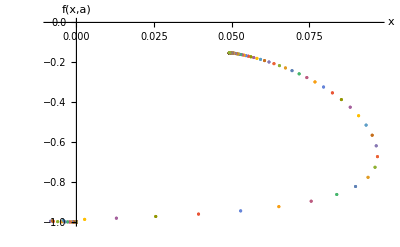

```mathematica
(*Plot the solution*)
EinsteinPlotKOpen=ListPlot[EinsteinPointSolutionsKOpenFull,AxesLabel->{"x","f(x,a)"},PlotRange->Full]
```

#### 3-D x-Y-Z Phase Space

```mathematica
(*Define a constant curvature hypersurface*)
K=KOpen;
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
trajConstantKOpen[Z0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==Z0}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(0.133333+(0.333333 Z0)/(1.-1. Z0)) β)/(√(1.13333+(0.333333 Z0)/(1.-1. Z0))) is not a number or a rectangular array of numbers.

```mathematica
solKOpen[1]=trajConstantKOpen[0.1,1]
```

NDSolve::ndcf: Repeated convergence test failure at t == -2.42185; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solKOpen[2]=trajConstantKOpen[0.1,-1]
```

NDSolve::mxst: Maximum number of 789772 steps reached at the point t == 2.42364.

{{X1→InterpolatingFunction[{{-100., 2.42364}}, <>],Y1→InterpolatingFunction[{{-100., 2.42364}}, <>],Z1→InterpolatingFunction[{{-100., 2.42364}}, <>]}}

```mathematica
solKOpen[3]=trajConstantKOpen[0.3,1]
```

NDSolve::mxst: Maximum number of 1657247 steps reached at the point t == -1.96589.

{{X1→InterpolatingFunction[{{-1.96589, 100.}}, <>],Y1→InterpolatingFunction[{{-1.96589, 100.}}, <>],Z1→InterpolatingFunction[{{-1.96589, 100.}}, <>]}}

```mathematica
solKOpen[4]=trajConstantKOpen[0.3,-1]
```

NDSolve::mxst: Maximum number of 1657247 steps reached at the point t == 2.30062.

{{X1→InterpolatingFunction[{{-100., 2.30062}}, <>],Y1→InterpolatingFunction[{{-100., 2.30062}}, <>],Z1→InterpolatingFunction[{{-100., 2.30062}}, <>]}}

```mathematica
solKOpen[5]=trajConstantKOpen[0.5,1]
```

NDSolve::mxst: Maximum number of 2289409 steps reached at the point t == -2.12002.

{{X1→InterpolatingFunction[{{-2.12002, 100.}}, <>],Y1→InterpolatingFunction[{{-2.12002, 100.}}, <>],Z1→InterpolatingFunction[{{-2.12002, 100.}}, <>]}}

```mathematica
solKOpen[6]=trajConstantKOpen[0.5,-1]
```

NDSolve::mxst: Maximum number of 2289409 steps reached at the point t == 2.07022.

{{X1→InterpolatingFunction[{{-100., 2.07022}}, <>],Y1→InterpolatingFunction[{{-100., 2.07022}}, <>],Z1→InterpolatingFunction[{{-100., 2.07022}}, <>]}}

```mathematica
(*Plot each trajectory*)
```

```mathematica
PhaseSpaceConstantKOpen[1]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKOpen[1],{t,-2.41,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKOpen[2]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKOpen[2],{t,-100,2.41},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKOpen[3]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKOpen[3],{t,-1.96,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKOpen[4]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKOpen[4],{t,-100,2.29},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKOpen[5]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKOpen[5],{t,-2.11,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceConstantKOpen[6]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.solKOpen[6],{t,-100,2.06},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantKOpenPlots=Table[PhaseSpaceConstantKOpen[i],{i,1,6}];
```

```mathematica
(*Show all components of the phase space*)
xYzc3=Show[trajConstantKOpenPlots,FPShowXYZ,CompactFPShowXYZ,AccnXYZ,AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},PlotRange->{{0,1},{-1.1,1.1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## 2-D x-Y Projection

```mathematica
(*Plot the trajectories defined above on the X-Y plane*)
```

```mathematica
PhaseSpaceConstantKOpenXY[1]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKOpen[1],{t,-2.41,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500];
```

```mathematica
PhaseSpaceConstantKOpenXY[2]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKOpen[2],{t,-100,2.41},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500];
```

```mathematica
PhaseSpaceConstantKOpenXY[3]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKOpen[3], {t,-1.96,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500];
```

```mathematica
PhaseSpaceConstantKOpenXY[4]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKOpen[4], {t,-100,2.29},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500];
```

```mathematica
PhaseSpaceConstantKOpenXY[5]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKOpen[5],{t,-2.11,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500];
```

```mathematica
PhaseSpaceConstantKOpenXY[6]=ParametricPlot[Evaluate[{X1[t],Y1[t]}/.solKOpen[6], {t,-100,2.06},PlotStyle -> {{Gray , Opacity[0.75]}}],AxesLabel->{"X","Y"},PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceConstantKOpenProjection=Table[PhaseSpaceConstantKOpenXY[i],{i,1,6}];
```

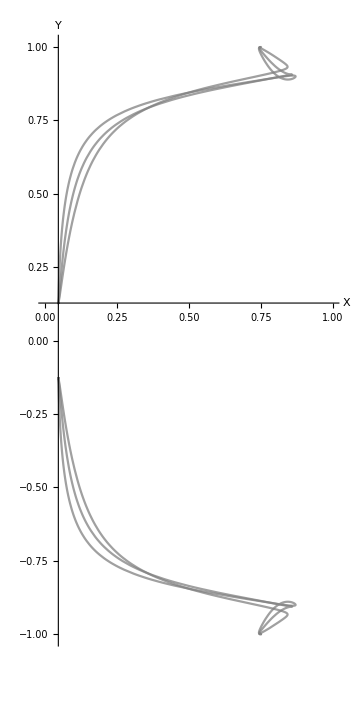

```mathematica
(*Show all the trajectories on the same plot*)
Show[PhaseSpaceConstantKOpenProjection,PlotRange->{{0,1},{-1,1}}]
```